## Caustics and al

```mathematica
ac = (δ-b^2)a/c^2
bc = (a^2-δ)b/c^2
oR2=Factor@FullSimplify[ac^2+bc^2,c>0&&a>0&&b>0]
```

(a (-b^2+δ))/c^2

(b (a^2-δ))/c^2

(a^4 b^2+a^2 b^4-4 a^2 b^2 δ+a^2 δ^2+b^2 δ^2)/c^4

```mathematica
oR2=FullSimplify[oR/.{δ->Sqrt[a^4-a^2 b^2+b^4]},c>0&&a>0&&b>0]
```

oR

```mathematica
oR3[a_,b_]=FullSimplify[oR2^2/.c->Sqrt[a^2-b^2]]
```

oR^2

```mathematica
Plot[oR3[a,1],{a,1.1,2}]
```

-Graphics-

## Cushion Region between two identical ellipses

```mathematica
Clear@elly;Clear@a;Clear@x;Clear@y;
elly[a_,x_]:=Sqrt[1-(x/a)^2];
```

```mathematica
xsol[a_]=FullSimplify[x/.First@Solve[elly[a,x]==x,x,Reals],a>1]
```

a/(√(1+a^2))

```mathematica
areaCentralSquare[a_]=FullSimplify[(2xsol[a])^2,a>1]
```

(4 a^2)/(1+a^2)

```mathematica
calota[a_]=FullSimplify[Integrate[elly[a,x]-xsol[a],{x,-xsol[a],xsol[a]},Assumptions->a>1],a>1]
```

a (-a/(1+a^2)+ArcCsc[√(1+a^2)])

```mathematica
areaCushion[a_]=FullSimplify[areaCentralSquare[a]+4calota[a],a>1]
```

4 a ArcCsc[√(1+a^2)]

```mathematica
FullSimplify[areaCushion[(1+Sqrt@5)/2]]
```

2 (1+√5) ArcCsc[√(1/2 (5+√5))]

```mathematica
Clear@areaCushionNum;
areaCushionNum[a_]:=Module[{a2=a*a},Area[ImplicitRegion[(x^2+a2 y^2≤a2)&&(a2 x^2+y^2≤a2),{x,y}]]]
```

```mathematica
areaCushion[2]
```

8 ArcCsc[√5]

```mathematica
areaCushionNum[2.]
```

3.70918

```mathematica
areaCushionToEll[a_]=areaCushion[a]/(π a)
```

(4 ArcCsc[√(1+a^2)])/π

```mathematica
FullSimplify[areaCushionToEll[(1+Sqrt[5])/2]]
```

(4 ArcCsc[√(1/2 (5+√5))])/π

```mathematica
N[areaCushionToEll[(1+Sqrt[5])/2]]
```

0.704833

```mathematica
areaCushionToEll[1.]
```

1.

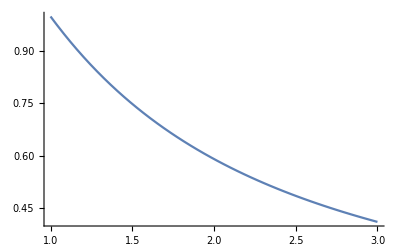

```mathematica
Plot[areaCushionToEll[a],{a,1,3}]
```

```mathematica
2./(1+Sqrt[5])
```

0.618034

#### What is the “a” required for an area ratio of "k"

```mathematica
areaRatioK[k_]=FullSimplify[a/.Second@Solve[areaCushionToEll[a]==k,a],0<k<1]
```

Cot[(k π)/4]

#### The "a" required so the cushion is 1/2 the area of the ellipse is 1+Sqrt[2]

```mathematica
areaRatioK[1/2]
```

Cot[π/8]

```mathematica
areaRatioK[1./2]-Sqrt[2]
```

1.

```mathematica
FullSimplify[areaCushionToEll[1+Sqrt@2]]
```

1/2

```mathematica
FindRoot[areaCushionToEll[a]-2/(1+Sqrt[5]),{a,2}]
```

{a→1.89574}

#### The expression for the corner (x, y) at aspect ratio 1+Sqrt[2] contains three number 2' s

```mathematica
xharm=FullSimplify@xsol[1+Sqrt@2]
```

(√(2+√2))/2

```mathematica
N[xharm,10]
```

0.9238795325

#### What is the circle radius which goes thru the cushion’s 4 corners

```mathematica
ellCircRad[a_]=Sqrt[2]xsol[a]
```

(√2 a)/(√(1+a^2))

```mathematica
FullSimplify@ellCircRad[1+Sqrt@2]
```

√(1+1/(√2))

```mathematica
N@%
```

1.30656

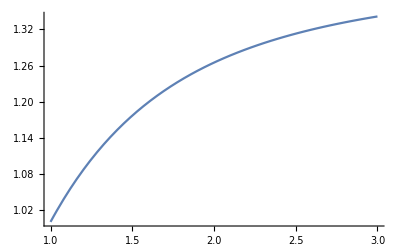

```mathematica
Plot[ellCircRad[a],{a,1,3}]
```

```mathematica
drawTwoElls[a_]:=Module[{ell1,ell2,a2=a*a,rp,gr,xs,ell3,r,c,fs},
c=Sqrt[a^2-1];
fs={{-c,0},{c,0},{0,-c},{0,c}};
ell1={Blue,Circle[{0,0},{a,1}]};
ell2={Blue,Circle[{0,0},{1,a}]};
r=ellCircRad[a];
ell3={Red,Circle[{0,0},r]};
rp=RegionPlot[(x^2+a2 y^2≤a2)&&(a2 x^2+y^2≤a2),{x,-a,a},{y,-a,a}];
xs=xsol[a];
gr=Graphics[{PointSize@Large,
ell1,ell2,ell3,Point@{{xs,xs},{-xs,xs},{-xs,-xs},{xs,-xs}},Blue,Point@fs,Dashed,Line@{fs[[2]],fs[[4]]}}];
Show[{rp,gr}]];
```

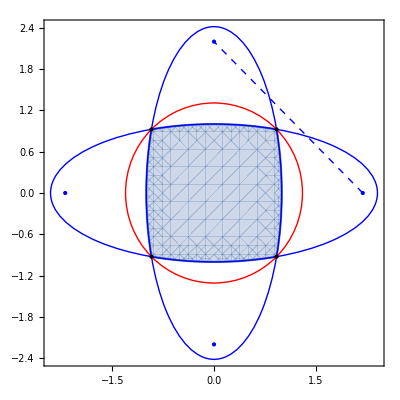

```mathematica
drawTwoElls[1+Sqrt@2]
```

#### What is the "a" such that the line connecting foci goes thru a corner (i.e., it is collinear -- vanishing determinant)

```mathematica
Module[{xs=xsol[a],c,fl,ft,det},
c=Sqrt[a^2-1];
fl={c,0,1};
ft={0,c,1};
det=Det[{{xs,xs,1},fl,ft}];
a/.Solve[det==0,a]]
```

{-1,1,ⅈ √(-2+√5),√(2+√5)}

```mathematica
N[Sqrt[2+Sqrt[5]]]
```

2.05817

#### Nice result : when the interfocal line goes thru a corner, the radius of the circle is Sqrt[ϕ] and the aspect ratio a=Sqrt[1+2ϕ]

```mathematica
FullSimplify[ellCircRad[Sqrt[2+Sqrt[5]]]]
```

√(1/2 (1+√5))

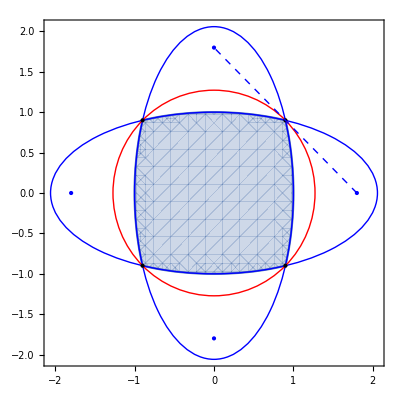

```mathematica
drawTwoElls[Sqrt[2+Sqrt[5]]]
```

```mathematica
areaCushion[Sqrt[2+Sqrt[5]]]
```

4 √(2+√5) ArcCsc[√(3+√5)]

```mathematica
N@areaCushionToEll[Sqrt[2+Sqrt[5]]]
```

0.575859

#### What the aspect ratio such that the circle which goes thru the corners also goes thru the 4 foci?

```mathematica
a/.Solve[ellCircRad[a]==Sqrt[a^2-1],a]
```

{-ⅈ √(-1+√2),ⅈ √(-1+√2),-√(1+√2),√(1+√2)}

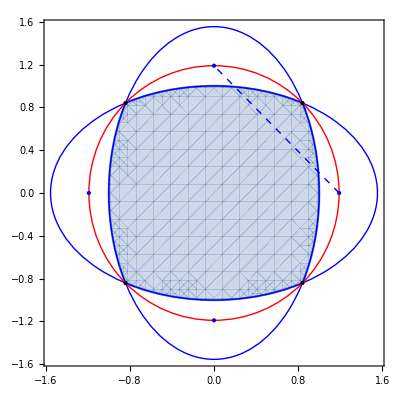

```mathematica
drawTwoElls[Sqrt[1+Sqrt[2]]]
```

```mathematica
N[{π (Sqrt[2]),π Sqrt[1+Sqrt[2]]}]
```

{4.44288,4.88132}

```mathematica
FullSimplify[areaCushion[Sqrt[1+Sqrt[2]]]]
```

4 √(1+√2) ArcCsc[√(2+√2)]

```mathematica
FullSimplify[areaCushionToEll[Sqrt[1+Sqrt[2]]]]
```

(4 ArcCsc[√(2+√2)])/π

#### What is the aspect ratio such that the cushion goes thru the foci: Sqrt[2]

```mathematica
Solve[Sqrt[a^2-1]==1]
```

{{a→-√2},{a→√2}}

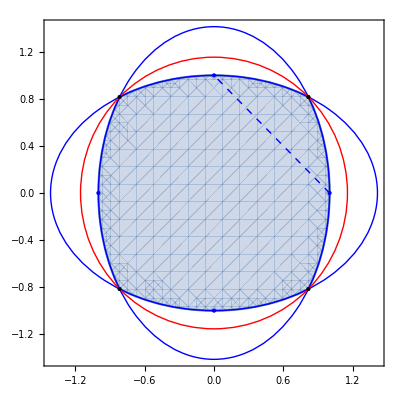

```mathematica
drawTwoElls[Sqrt@2]
```

```mathematica
areaCushion[Sqrt@2]
```

4 √2 ArcCsc[√3]

```mathematica
areaCushionToEll[Sqrt@2]
```

(4 ArcCsc[√3])/π

```mathematica
N[%]
```

0.783653

```mathematica
ellCircRad[Sqrt@2]
```

2/(√3)

```mathematica
ellCircRad[Sqrt@2]/Sqrt@2
```

√(2/3)

```mathematica
FullSimplify[areaCushion[Sqrt@2]/( π ellCircRad[Sqrt@2]^2)]
```

(3 √2 ArcCsc[√3])/π